#### Eigenvalue problem:

#### Building the Circuit

First we try the simplest Unitary with a single CNOT

#Q=4

```mathematica
θ=Pi/4;
XRow=SparseArray@KroneckerProduct[RX[θ],RX[θ],RX[θ],RX[θ]];
ZRow=SparseArray@KroneckerProduct[RZ[θ],RZ[θ],RZ[θ],RZ[θ]];
UOdd=SparseArray@KroneckerProduct[CNOT,CNOT];
UEven=SparseArray@KroneckerProduct[IdentityMatrix[2],CNOT,IdentityMatrix[2]];
U=SparseArray@XRow.ZRow.UEven.ZRow.XRow.ZRow.UOdd.ZRow;
```

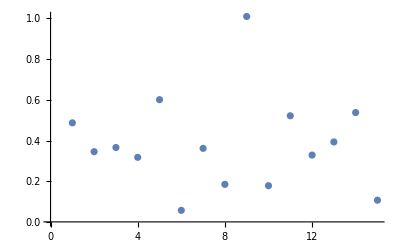

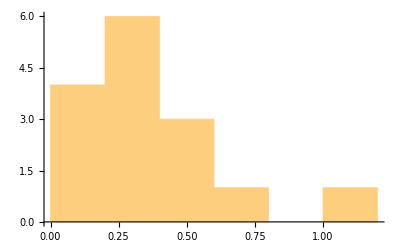

```mathematica
A=Sort[Log[N[Eigenvalues[U]]]/-I,Re[#1]>Re[#2]&];
LS=ConstantArray[0,{Length@A-1}];
For[n=1,n<Length@A,n++,LS[[n]]=A[[n]]-A[[n+1]]]
ListPlot[LS]
Histogram[LS]
```

#Q=6

```mathematica
θ=Pi/4;
XRow=SparseArray@KroneckerProduct[RX[θ],RX[θ],RX[θ],RX[θ],RX[θ],RX[θ]];
ZRow=SparseArray@KroneckerProduct[RZ[θ],RZ[θ],RZ[θ],RZ[θ],RZ[θ],RZ[θ]];
UOdd=SparseArray@KroneckerProduct[CNOT,CNOT,CNOT];
UEven=SparseArray@KroneckerProduct[IdentityMatrix[2],CNOT,CNOT,IdentityMatrix[2]];
U=SparseArray@XRow.ZRow.UEven.ZRow.XRow.ZRow.UOdd.ZRow;
```

```mathematica
A=Sort[Log[N[Eigenvalues[U]]]/-I,Re[#1]>Re[#2]&];
LS=ConstantArray[0,{Length@A-1}];
For[n=1,n<Length@A,n++,LS[[n]]=A[[n]]-A[[n+1]]]
ListPlot[LS]
Histogram[LS]
```

$Aborted

-Graphics-

-Graphics-